```mathematica
numberOfContainers=35;
numberOfPlatforms=10;
numberOfPreferences=2;
numberOfBatches=3;
```

```mathematica
(*если на контейнер можно поставить от 1 до k контейнеров, то сумма всех вариантов расстановок:*)
Sum[Binomial[numberOfContainers,k]*k!,{k,3}]
```

40495

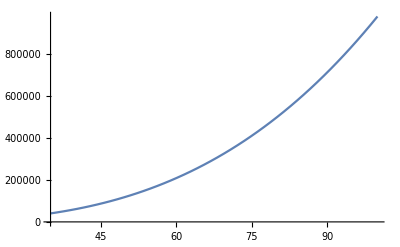

```mathematica
Plot[Sum[Binomial[numberOfContainers,k]*k!,{k,3}],{numberOfContainers,35,100}]
```

```mathematica
(*сгенерируем всевозможные подмножества для контейнеров*)
subsets=Subsets[Range@numberOfContainers,{2,3}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},7095,{29,33,35},{29,34,35},{30,31,32},{30,31,33},{30,31,34},{30,31,35},{30,32,33},{30,32,34},{30,32,35},{30,33,34},{30,33,35},{30,34,35},{31,32,33},{31,32,34},{31,32,35},{31,33,34},{31,33,35},{31,34,35},{32,33,34},{32,33,35},{32,34,35},{33,34,35}}
 |  |  |  |

```mathematica
subsets//Length
```

7140

```mathematica
(*поставим в соответствие приоритеты*)
RandomVariate@MultinomialDistribution[numberOfContainers,ConstantArray[1/#,#]&@numberOfPreferences]
```

{18,17}

```mathematica
(*следовательно, 16 контейнеров первого приоритета и 19 контейнеров 2 приоритета*)
```

```mathematica
step1=RandomVariate@MultinomialDistribution[numberOfContainers,ConstantArray[1/#,#]&@20]
```

{1,4,2,5,1,1,4,2,1,2,2,2,2,0,0,3,1,0,2,0}

```mathematica
RandomInteger[{1,20},numberOfContainers]
```

{16,4,17,9,14,4,8,6,20,9,13,15,16,17,8,6,13,1,7,13,16,15,19,2,6,10,2,4,6,20,15,17,16,1,14}

```mathematica
RandomSample@Flatten@MapIndexed[ConstantArray[#2⟦1⟧,#1]&,DeleteCases[step1,0]]
```

{9,14,3,7,12,14,4,13,13,2,8,10,4,2,16,5,2,8,6,7,7,16,4,14,15,12,10,3,4,4,2,7,1,11,11}

```mathematica
Transpose[{Range@numberOfContainers,%}](*у первого приоритета 11 контейнеров,у второго приоритета 3 контейнера и тд*)
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«25»},Null} cannot be transposed.

Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35},Null}]

```mathematica
getVariant=RandomVariate@MultinomialDistribution[numberOfContainers,ConstantArray[1/#,#]&@#]&;
getCharacterictics=RandomSample@Flatten@MapIndexed[ConstantArray[#2⟦1⟧,#1]&,DeleteCases[#,0]]&;
```

```mathematica
priors=getCharacterictics@getVariant@numberOfPreferences (*список приоритетов*)
```

{1,1,1,1,1,1,1,1,2,2,1,2,1,2,2,2,1,1,2,2,1,2,1,2,2,1,2,1,1,2,2,1,2,1,1}

```mathematica
batches=getCharacterictics@getVariant@numberOfBatches -1(*список партий*)
```

{0,2,2,2,2,1,2,2,0,0,1,1,2,0,2,2,2,0,2,1,1,0,2,2,2,2,0,1,2,0,2,2,0,0,2}

```mathematica
shape=0.5; (*доля*)
feasibleSubsetsForPlatforms=Table[RandomSample[subsets,RandomInteger[{1,Floor[shape*Length@subsets]}]],{p,numberOfPlatforms}];
(*но мы можем случайно получить вариант, где какой то из контейнеров не будет задействован*)
```

```mathematica
containers=Union@Flatten@feasibleSubsetsForPlatforms (*все контейнеры, которые были взяты для рассмотрения на расстоновки*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

```mathematica
(*контейнер, приоритет, партия*)
Transpose[{containers,priors,batches}]
```

{{1,1,0},{2,1,2},{3,1,2},{4,1,2},{5,1,2},{6,1,1},{7,1,2},{8,1,2},{9,2,0},{10,2,0},{11,1,1},{12,2,1},{13,1,2},{14,2,0},{15,2,2},{16,2,2},{17,1,2},{18,1,0},{19,2,2},{20,2,1},{21,1,1},{22,2,0},{23,1,2},{24,2,2},{25,2,2},{26,1,2},{27,2,0},{28,1,1},{29,1,2},{30,2,0},{31,2,2},{32,1,2},{33,2,0},{34,1,0},{35,1,2}}

```mathematica
(*другая форма записи, 0 партия = отсутствие партии*)
setOfContainers=Association[#⟦1⟧-><|"Приоритет"->#⟦2⟧,"Партия"->#⟦3⟧|>&/@Transpose[{containers,priors,batches}]]
```

<|1→<|Приоритет→1,Партия→0|>,2→<|Приоритет→1,Партия→2|>,3→<|Приоритет→1,Партия→2|>,4→<|Приоритет→1,Партия→2|>,5→<|Приоритет→1,Партия→2|>,6→<|Приоритет→1,Партия→1|>,7→<|Приоритет→1,Партия→2|>,8→<|Приоритет→1,Партия→2|>,9→<|Приоритет→2,Партия→0|>,10→<|Приоритет→2,Партия→0|>,11→<|Приоритет→1,Партия→1|>,12→<|Приоритет→2,Партия→1|>,13→<|Приоритет→1,Партия→2|>,14→<|Приоритет→2,Партия→0|>,15→<|Приоритет→2,Партия→2|>,16→<|Приоритет→2,Партия→2|>,17→<|Приоритет→1,Партия→2|>,18→<|Приоритет→1,Партия→0|>,19→<|Приоритет→2,Партия→2|>,20→<|Приоритет→2,Партия→1|>,21→<|Приоритет→1,Партия→1|>,22→<|Приоритет→2,Партия→0|>,23→<|Приоритет→1,Партия→2|>,24→<|Приоритет→2,Партия→2|>,25→<|Приоритет→2,Партия→2|>,26→<|Приоритет→1,Партия→2|>,27→<|Приоритет→2,Партия→0|>,28→<|Приоритет→1,Партия→1|>,29→<|Приоритет→1,Партия→2|>,30→<|Приоритет→2,Партия→0|>,31→<|Приоритет→2,Партия→2|>,32→<|Приоритет→1,Партия→2|>,33→<|Приоритет→2,Партия→0|>,34→<|Приоритет→1,Партия→0|>,35→<|Приоритет→1,Партия→2|>|>

```mathematica
(*расстояния*)
distance=AssociationThread[#,RandomReal[{0,100},Length@#]]&@DeleteDuplicates@Flatten[feasibleSubsetsForPlatforms,1]
```

<|{8,13,21}→82.4583,{19,22,24}→82.8236,{3,9,12}→90.9523,{3,6}→48.9104,{3,13,16}→67.9925,{20,25,35}→67.4281,{13,15,27}→69.97,{11,21,33}→21.7466,{4,5,16}→3.65399,6799,{4,24,27}→51.8688,{3,5,7}→39.8212,{8,20,35}→65.6041,{5,13,32}→71.7558,{15,25}→48.02,{3,11,19}→70.9154,{4,9,28}→40.9754,{6,17,34}→73.7795|>
 |  |  |  |

```mathematica
(*списки контейнеров, которые принадлежат каждому из приоритетов*)
setsForPriors=GroupBy[containers,setOfContainers[#,"Приоритет"]&]
```

<|1→{1,2,3,4,5,6,7,8,11,13,17,18,21,23,26,28,29,32,34,35},2→{9,10,12,14,15,16,19,20,22,24,25,27,30,31,33}|>

```mathematica
(*аналогично с партиями, исключая беспартийников*)
```

```mathematica
setsForBatches=KeyDrop[GroupBy[containers,setOfContainers[#,"Партия"]&],0]
```

<|2→{2,3,4,5,7,8,13,15,16,17,19,23,24,25,26,29,31,32,35},1→{6,11,12,20,21,28}|>